```mathematica
f[x_] = Cot[1.5*x] -2.3*x+0.8
```

0.8-2.3 x+Cot[1.5 x]

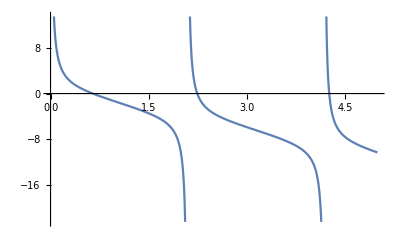

```mathematica
Plot[f[x],{x,0,5}]
```

```mathematica
FindRoot[f[x],{x,0.5}]
```

{x→0.646217}

```mathematica
FindRoot[f[x],{x,4.3}]
```

{x→0.646217}

```mathematica
fi1[x_] = (Cot[1.5*x]+0.8)/2.3
```

0.434783 (0.8+Cot[1.5 x])

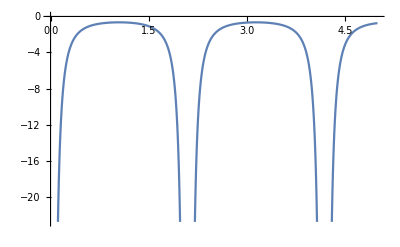

```mathematica
Plot[fi1'[x],{x,0,5}]
```

```mathematica
fi1'[0.646216805181774]
```

-0.959352

```mathematica
fi2[x_] =ArcCot[2.3*x- 0.8]/1.5
```

-0.666667 ArcCot[0.8-2.3 x]

```mathematica
TrigToExp[-0.6666666666666666 ArcCot[0.8-2.3 x]]
```

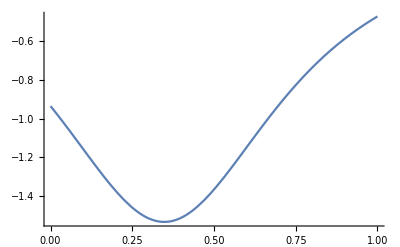

```mathematica
Plot[fi2'[x],{x,0,1}]
```